σ=14.1784≈10Sqrt[2]
μ=31.7454≈10Sqrt[10]
α=5.0131≈5
β=6.33248≈20/Sqrt[10]
max value at=25.4129

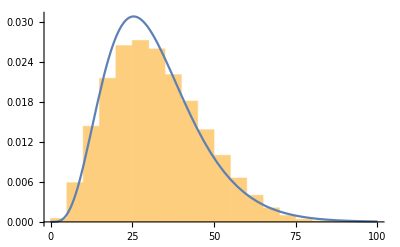

```mathematica
data :=Import["test_match_duration.txt", "List"]
σ=StandardDeviation[data];
μ=Mean[data];
α=μ^2/σ^2;
β=σ^2/μ;
Print["σ=", N[σ], "≈10Sqrt[2]\nμ=", N[μ], "≈10Sqrt[10]\nα=", N[α], "≈5\nβ=", N[β], "≈20/Sqrt[10]\nmax value at=", N[β(α-1)]]
Show[Histogram[data,Automatic,"ProbabilityDensity"],Plot[PDF[ℋ["FittedDistribution"],x],{x,0,100},PlotStyle->Thick], Plot[PDF[GammaDistribution[α, β],x],{x, 0, 100}]] 
(*, Plot[PDF[NormalDistribution[μ,σ],x],{x, 0, 100}]]*)
```